```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
Needs["SSSiCv100`"];
```

Visually, SSS networks can be identified as 1-dimensional, 2-dimensional, etc. Ex/

But we want the program to identify the dimension automatically, by considering the patterns of the node numbers.

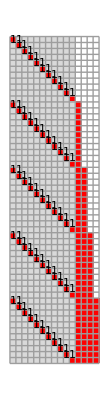



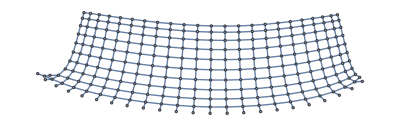
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
SSSDisplay[sss3,Min->1,Max->255,SSSMin->Automatic,SSSMax->55,NetMin->Automatic,NetMax->Automatic,HighlightMethod->Number,RulePlacement->Bottom,NetMethod->{GraphPlot},ImageSize->287.,NetSize->{Automatic,300},SSSSize->{Automatic,288.},IconSize->{Automatic,20},VertexSize->Automatic,VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->False]
```

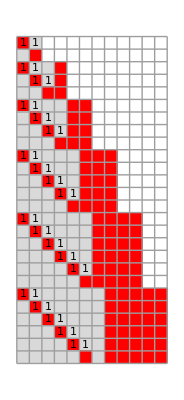
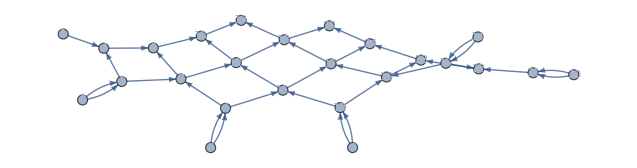
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
SSS[{"BA"->"AB",""->"BA"},"BA",25];
```

1. Start with a list of event/node indices, either from the SSS or from the network. These should be special in some way.
2. Create a table of nth-differences from the list. If row k is constant, the dimension of the original data is k.

Original arbitrary data, which we can immediately identify as a list of squares: 1 4 9 16 25 36 49

Tables of differences

1 4 9 16 25 36 49

3 5 7 9 11 13

2 2 2 2 2

We call the initial data row 0, the first row of differences is row 1, etc. Since the first constant row is row 2, this data should be identified as 2-dimensional, which agrees with the exponent of 2 (squares) in the zformula for the data: y = x^2. Similarly, forming a table of differences starting with data generated by any polynomial formula, y = cxn + ..., will end up with a constant n-th row.

No row in the difference table of an exponential network ever becomes constant (nor even a straight line), just as repeated derivatives of exponential functions are all exponentials, never constant. To identify them we take ratios of neighboring elements in the rows of the difference table. If any row of this ratio table becomes an integer constant, all further rows will also be constant, and exponential behavior is demonstrated. The constant found is the average out-degree of nodes of the network -- the number of graph branches leading out from the nodes.

Problems:

1. Initial irregularities before the pattern sets in. How to decide how much to ignore?
2. Fractional dimension in the difference table: no row is exactly constant, but the slope of the best fit lines changes from positive to negative, and then the values begin to fluctuate ever more wildly. The point where this happens approximates the dimension, but somehow we need to be able to calculate the fractional part.
3. Fractional exponential dimension: if, for example, half the nodes have out-degree 2 and half have 3, the average is 2.5, and the constant should be 2.5, but in fact the rows don’t exactly become 2.5, only close, and then start to fluctuate again.

Possible solutions:
1. Ignore first 10% of the data to try to get past initial irregularities. If irregularities persist, try further evolution: in theory, the irregular portion will eventually be included in the 10%.
2. Try summing pairs, triples, etc., in the data and difference rows, to smooth out fluctuations.
3. Fit the initial data row to y = cx^n and to y = cn^x, and see which gives the best fit (R-squared value closest to 1). Problem: not a straight line due to additional terms in the formula.
4. Fit to each row of the differences table in turn until we get an R-squared value that is better than the following row. The fit should keep getting better as additional polynomial terms disappear with successive differences.
5. (If using a network: Turn the network (with edges of the form n --> m) into a list of sets of edge/link lengths, as we have been doing.) But then rather than simply taking repeated differences of adjacent terms or terms having some fixed separation (the triangular patterns above), at each “level” form the nth differences for terms separated by 0, 1, 2, …, terms. So rather than an upside down triangle, we’ll have an upside down tetrahedron, with each level being a triangle. If at some row m of some level n we come to a lot of 0 entries, that was a productive choice for m and n: the pattern is revealed by subtracting terms separated by m neighbors, a constant row reached after n - 1 differences, a 0 row after n differences, indicating dimension n - 1. 
.